Carbapenem Resistance Model:

Objective: Whereas a clear correlation exists between consumption of antibiotics and the evolution of resistance in microbial communities, the effect of reduction of usage is less clear. To project the future frequency of carbapenem resistance, based on yearly surveillance data and consumption data. A population genetic model was adapted to retrospectively estimate the relationship between evolutionary fitness of carbapenem resistance and carbapenem consumption.

Derivation: We fit the historical selection to consumption via a deterministic, continuous-time haploid model of the frequency of resistance. See, for reference: 1) Hartl, Daniel L., Andrew G. Clark, and Andrew G. Clark. Principles of population genetics. Vol. 116. Sunderland: Sinauer associates, 1997—base population genetic model; 2) Nielsen, K. M., & Townsend, J. P. (2004). Monitoring and modeling horizontal gene transfer. Nature biotechnology, 22(9), 1110-1114—relation of base model to novel DNA such as antimicrobial resistance elements; and 3) Johnsen, P. J., Townsend, J. P., Bøhn, T., Simonsen, G. S., Sundsfjord, A., & Nielsen, K. M. (2011). Retrospective evidence for a biological cost of vancomycin resistance determinants in the absence of glycopeptide selective pressures. Journal of antimicrobial chemotherapy, 66(3), 608-610 —application of base model to project future vancomycin resistance after ban of use.

```mathematica
ClearAll["Global`*"]
```

```mathematica
r[t_,p0_,a_]:=ⅇ^(a*t)/((1/p0)-1+ⅇ^(a *t)) ; 
r1[t_,p0_,a_]:=ⅇ^(a* Total[c[[1;;t]]])/((1/p0)-1+ⅇ^(a * Total[c[[1;;t]]])) ; 
r2[t_,p0_,a_,b_] := ⅇ^(a* Total[c[[1;;t]]]+b*(t- Total[c[[1;;t]]]))/((1/p0)-1+ⅇ^(a* Total[c[[1;;t]]]+b*(t- Total[c[[1;;t]]]))) ; 
r3[t_,p0_,a_,b_] := ⅇ^(a* Total[cn[[1;;t]]]+b*(Total[df[[1;;t]]]))/((1/p0)-1+ⅇ^(a*  Total[cn[[1;;t]]]+b*(Total[df[[1;;t]]]))) ; 
r3[10,0.3,2,3]
```

1.

Where r is the frequency of resistance at time t, p0 is the initial frequency of resistance, and a is the continuous time Malthusian selection coefficient

Below, we apply this model in a preliminary case to the United States.

```mathematica
Note that the likelihood function used here will additionally be improved from that used in the preliminary model above. Because surveillance is conducted by sampling and testing for resistance, likelihood can be quantified under better distributional assumptions, with greater accuracy and precision. Instead of the observed frequencies of resistance (which are not certain), likelihood can be calculated based on the observed cases of resistant (UKResistance, above) vs. non-resistant (UKIsolates – UKResistance, above) measured by surveillance—see for instance, Johnsen, P. J., Townsend, J. P., Bøhn, T., Simonsen, G. S., Sundsfjord, A., & Nielsen, K. M. (2011). Retrospective evidence for a biological cost of vancomycin resistance determinants in the absence of glycopeptide selective pressures. Journal of antimicrobial chemotherapy, 66(3), 608-610.
```

```mathematica
Load Data
```

Number of resistant isolates recovered, each year 2005–2014; Number of isolates tested, each year 2005–2014, estimated frequencies of resistance, 2005–2014.

```mathematica
SetDirectory[NotebookDirectory[]];
CountryName="United States";
Data=Import["DataSheet_cddep.xlsx",{"Data",CountryName}];
Years = Drop[Data[[1]],1];
tt = Length[Years];
c=Drop[Data[[2]],1];
Isolates=Drop[Data[[3]],1];
Resistance=Drop[Data[[4]],1];
RData=Resistance/Isolates;
cn = Drop[Data[[5]],1];
tc = Drop[Data[[6]],1];
df = tc-cn;
```

```mathematica
Maximum Likelihood Function
```

Likelihood function and plot: values for p0 are plotted along the x-axis (bottom), likelihood is quantified along the z-axis (left side), and amount of selection imposed per unit of consumption is plotted along the y-axis (top).

```mathematica
Lik[p0_,a_]:= Total[Table[Log[Binomial[Isolates[[j]],Resistance[[j]]]]+Resistance[[j]]*Log[r[j-1,p0,a]]+(Isolates[[j]]-Resistance[[j]])*Log[1-r[j-1,p0,a]],{j,1tt}]]
Lik1[p0_,a_]:= Total[Table[Log[Binomial[Isolates[[j]],Resistance[[j]]]]+Resistance[[j]]*Log[r1[j-1,p0,a]]+(Isolates[[j]]-Resistance[[j]])*Log[1-r1[j-1,p0,a]],{j,1tt}]]
Lik2[p0_,a_,b_]:= Total[Table[Log[Binomial[Isolates[[j]],Resistance[[j]]]]+Resistance[[j]]*Log[r2[j-1,p0,a,b]]+(Isolates[[j]]-Resistance[[j]])*Log[1-r2[j-1,p0,a,b]],{j,1,tt}]]
Lik2[0.2,0.9,0.1]
```

-13421.5

```mathematica
{max,{fittedp0,fitteda}}=NMaximize[{Lik[p0,a],0< p0< 1},{p0,a}]
{max1,{fittedp01,fitteda1}}=NMaximize[{Lik1[p0,a],0<p0< 1},{p0,a}]
{max2,{fittedp02,fitteda2,fittedb2}}=NMaximize[{Lik2[p0,a,b],0< p0< 1, 0≤a<1,0≤b<1},{p0,a,b}]
```

{-128.,{p0→0.000962493,a→0.415388}}

{-166.522,{p0→0.00238774,a→166.314}}

{-127.922,{p0→0.000960274,a→7.55803×10^-7,b→0.41643}}

Plot over time

```mathematica
Res=Transpose@{Years,RData};
t=Range[1,tt];
r1[2,fittedp01[[2]],fitteda1[[2]]]
x = Table[r1[j,fittedp01[[2]],fitteda1[[2]]],{j,1,tt}]
y = Table[r2[i,fittedp02[[2]],fitteda2[[2]],fittedb2[[2]]],{i,1,tt}]
ModelFit=Transpose@{Years,r[t,fittedp0[[2]],fitteda[[2]]]};
ModelFit1=Transpose@{Years,x};
ModelFit2=Transpose@{Years,y};
```

0.00350015

{0.00285861,0.00350015,0.00451071,0.00586511,0.00799079,0.0110675,0.0158533,0.0234666,0.0358048,0.0549139,0.0853494,0.132975,0.210658}

{0.00145491,0.00220365,0.003336,0.00504715,0.00762839,0.011514,0.0173426,0.0260417,0.0389283,0.0578114,0.0850387,0.123403,0.17573}

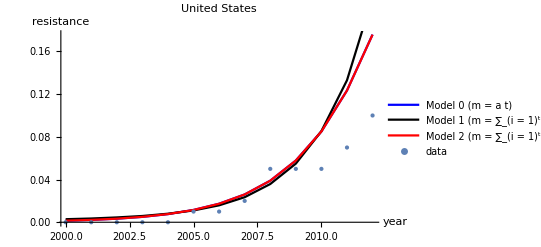

```mathematica
plot1=ListLinePlot[ModelFit, PlotStyle-> {Blue},AxesLabel->{year,resistance},PlotLabel-> "United States", PlotRange-> All,PlotLegends->{"Model 0 (m = a t)"}];
plot2 = ListLinePlot[ModelFit1, PlotStyle-> {Black},AxesLabel->{year,resistance},PlotLabel-> UnitedStates,PlotLegends->{"Model 1 (m = ∑_(i = 1)^t a p_i)"},PlotRange-> All];
plot3 = ListLinePlot[ModelFit2, PlotStyle-> {Red},AxesLabel->{year,resistance},PlotRange-> All,PlotLabel-> UnitedStates,PlotLegends->{"Model 2 (m = ∑_(i = 1)^t {a p_i-b (1-p_i)})"}];
plot=ListPlot[{Res}, PlotStyle-> PointSize[Large],PlotRange-> All,PlotLegends->{"data"}];

Show[plot1,plot2,plot3,plot]
```

Projections: